```mathematica
thumbnails=FileNames["*jpeg",FileNameJoin[{NotebookDirectory[],"art-thumbnails"}]];
```

```mathematica
Length[thumbnails]
```

190

```mathematica
imgs=FileNames["*jpeg",FileNameJoin[{NotebookDirectory[],"imgs"}]]
```

```mathematica
StringRiffle[Map[StringTemplate["'`1`'"],thumbnails],"\n"]//CopyToClipboard
```

```mathematica
Map[Export[#,Thumbnail[Import[#]]]&,thumbnails]
```

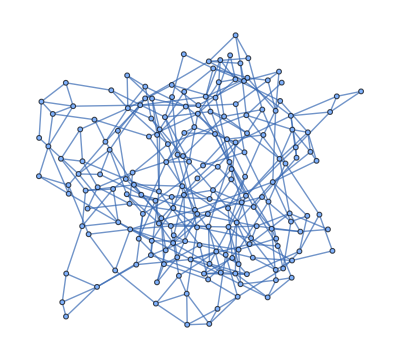

```mathematica
RandomGraph[WattsStrogatzGraphDistribution[190,.3]]
```

```mathematica
vertexRules=AssociationThread[ToString/@VertexList[]->Sort[Map[StringDelete[#,{DirectoryName[#],".jpeg"}]&,thumbnails]]];
```

```mathematica
Export[
FileNameJoin[{NotebookDirectory[],"graph","vertices.json"}],
vertexRules,"JSON"]
```

/Users/phileasdazeleygaist/Desktop/My Websites/sympoietic-art-organism/graph/vertices.json

```mathematica
Export[
FileNameJoin[{NotebookDirectory[],"graph","edges.json"}],
List@@@EdgeList[],"JSON"]
```

/Users/phileasdazeleygaist/Desktop/My Websites/sympoietic-art-organism/graph/edges.json